## Set Functions

```mathematica
SetDirectory[NotebookDirectory[]];
baseline100=Import["./EIR_100/0_0_0_0_100.csv"];
labels=baseline100[[1]]
requiredIndices={12,13,14,18};
labels[[requiredIndices]]
```

{,time,EL,EL_LAR,EL_BIO,EL_LAR_BIO,LL,LL_LAR,LL_BIO,LL_LAR_BIO,PL,SV,EV,IV,SH,IH,Mm,EIR,VC,R0}

{SV,EV,IV,EIR}

## Load 10

Load Data

```mathematica
(**)
levels0000=Import["./EIR_100/0_0_0_0_10.csv"][[2;;All,requiredIndices]];
levels7000=Import["./EIR_100/7_0_0_0_10.csv"][[2;;All,requiredIndices]];
levels7008=Import["./EIR_100/7_0_0_8_10.csv"][[2;;All,requiredIndices]];
levels7080=Import["./EIR_100/7_0_8_0_10.csv"][[2;;All,requiredIndices]];
levels7800=Import["./EIR_100/7_8_0_0_10.csv"][[2;;All,requiredIndices]];
levels7880=Import["./EIR_100/7_8_8_0_10.csv"][[2;;All,requiredIndices]];
levels7808=Import["./EIR_100/7_8_0_8_10.csv"][[2;;All,requiredIndices]];
levels7088=Import["./EIR_100/7_0_8_8_10.csv"][[2;;All,requiredIndices]];
levels7888=Import["./EIR_100/7_8_8_8_10.csv"][[2;;All,requiredIndices]];
dataList={levels0000,levels7000,levels7008,levels7080,levels7800,levels7880,levels7808,levels7088,levels7888};
orderedLabels={"[BASE]","[ITN]","[ITN,END]","[ITN,SPR]","[ITN,HOU]","[ITN,SPR,END]","[ITN,SPR,HOU]","[ITN,END,HOU]","[ITN,SPR,END,HOU]"};
```

EIR

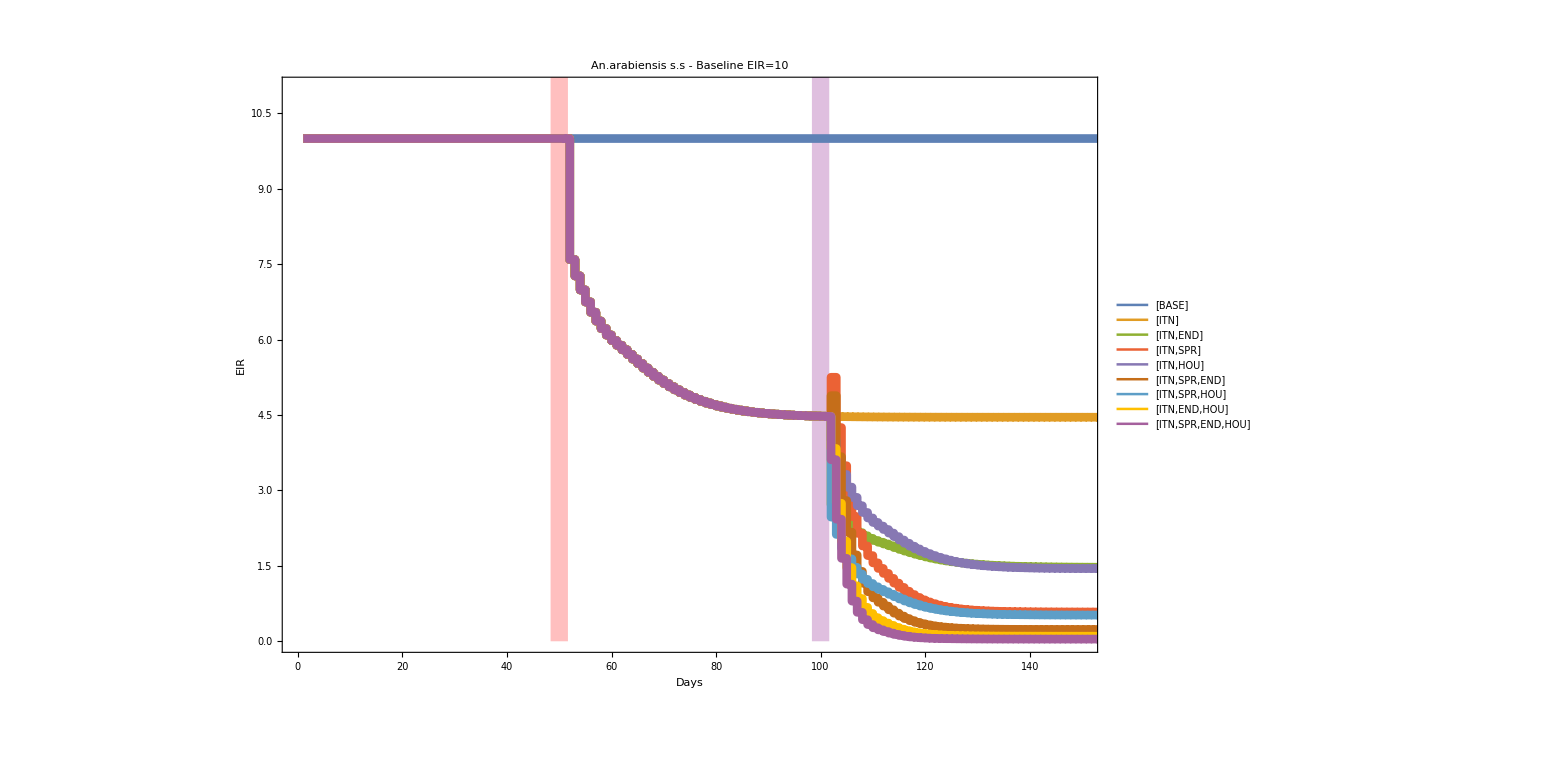

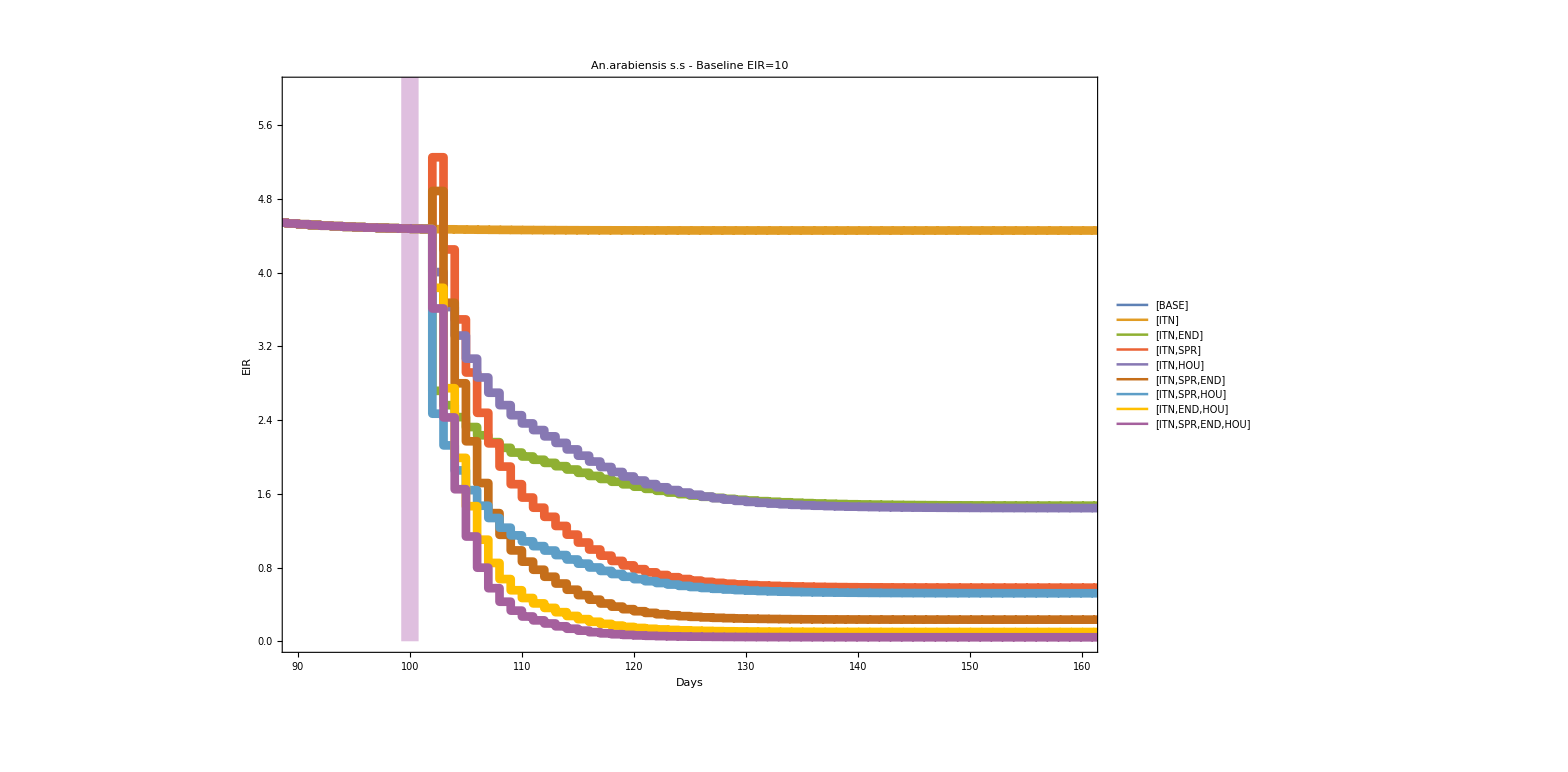

```mathematica
(**)
eirData=#[[All,4]]&/@dataList;
mosyData=(Total/@#[[All,1;;3]])&/@dataList;
(**)
ListLinePlot[eirData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{0,150},{0,11}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","EIR"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,10000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,10000}}]}
]
Export["AATimeSeries_Full.png",%,ImageResolution->300];
(**)
ListLinePlot[eirData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{90,160},{0,6}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","EIR"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,10000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,10000}}]}
]
Export["AATimeSeries_Zoom.png",%,ImageResolution->300];
```

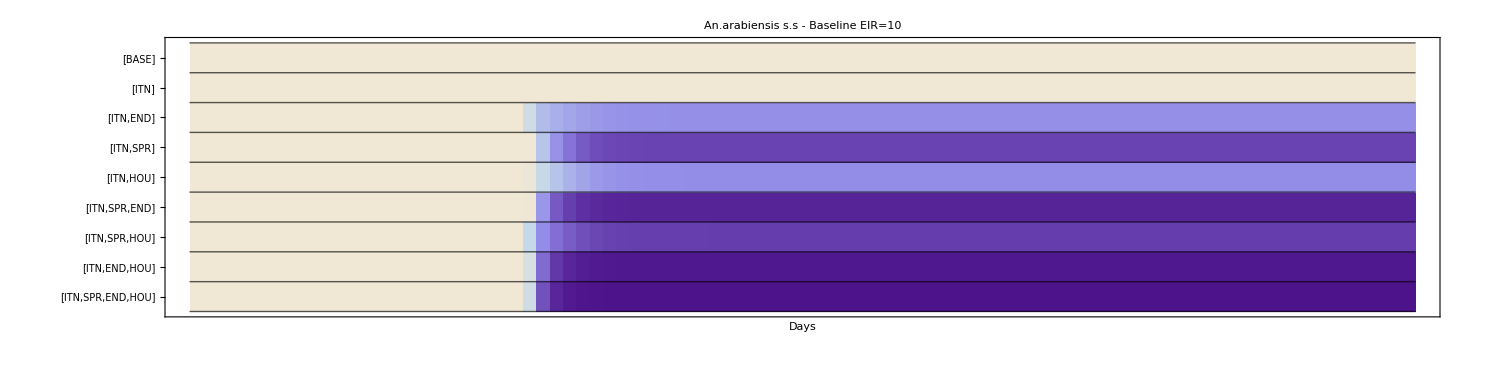

```mathematica
MatrixPlot[eirData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,4}]]&),
ColorFunctionScaling->False,
ImageSize->1500,
BaseStyle->Directive[20],
PlotLegends->Placed[Automatic,Below],
FrameTicks->{{Transpose[{Range[Length[orderedLabels]],orderedLabels}],None},{None,Automatic}},
AspectRatio->.25,
LabelStyle->20,
Mesh->{Table[{i,Directive[Thick,Black,Opacity[.65]]},{i,0,10}],None},
FrameLabel->{None,"Days"},
FrameStyle->Directive[Gray,Thickness[.005]](*,
Epilog->{Red,Opacity[.25],Thickness[.0075],Line[{{25,0},{25,100}}],Purple,Opacity[.25],Thickness[.0075],Line[{{100,0},{100,10000}}]}*)
]
Export["AATimeSeries_Matrix.png",%,ImageResolution->300];
```

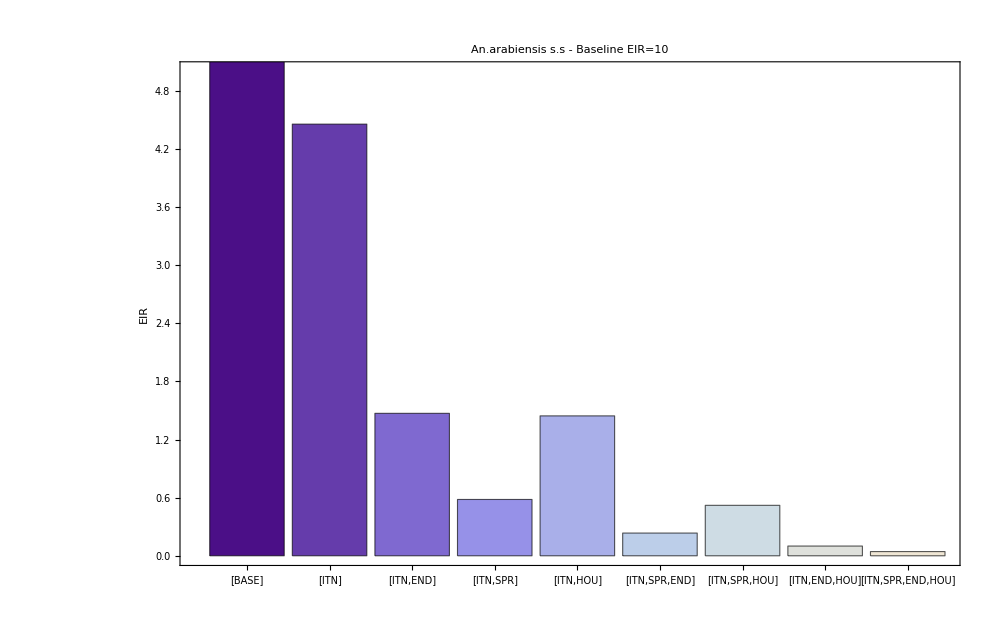

```mathematica
BarChart[Last/@eirData,
ChartStyle->{EdgeForm[Directive[Thick,Black,Opacity[.65]]],"LakeColors"},
ChartLabels->(Rotate[#,90Degree]&/@orderedLabels),
FrameStyle->Thickness[.0075],
BaseStyle->20,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameTicksStyle->20,
FrameLabel->{"","EIR"},
ImageSize->1000,
PlotRange->{0,5}
]
Export["AAHistogram.png",%,ImageResolution->300];
```

MOSSY

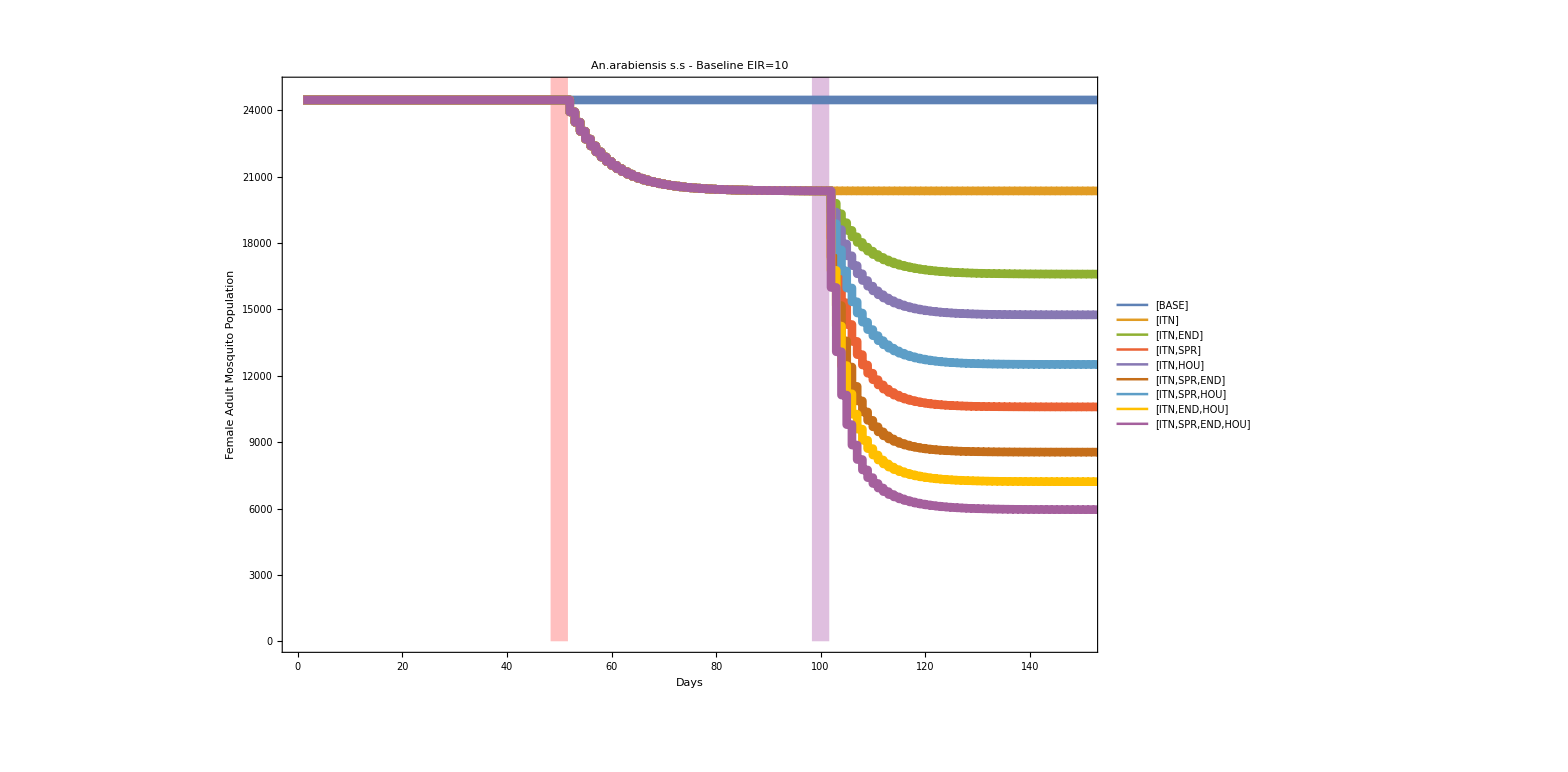

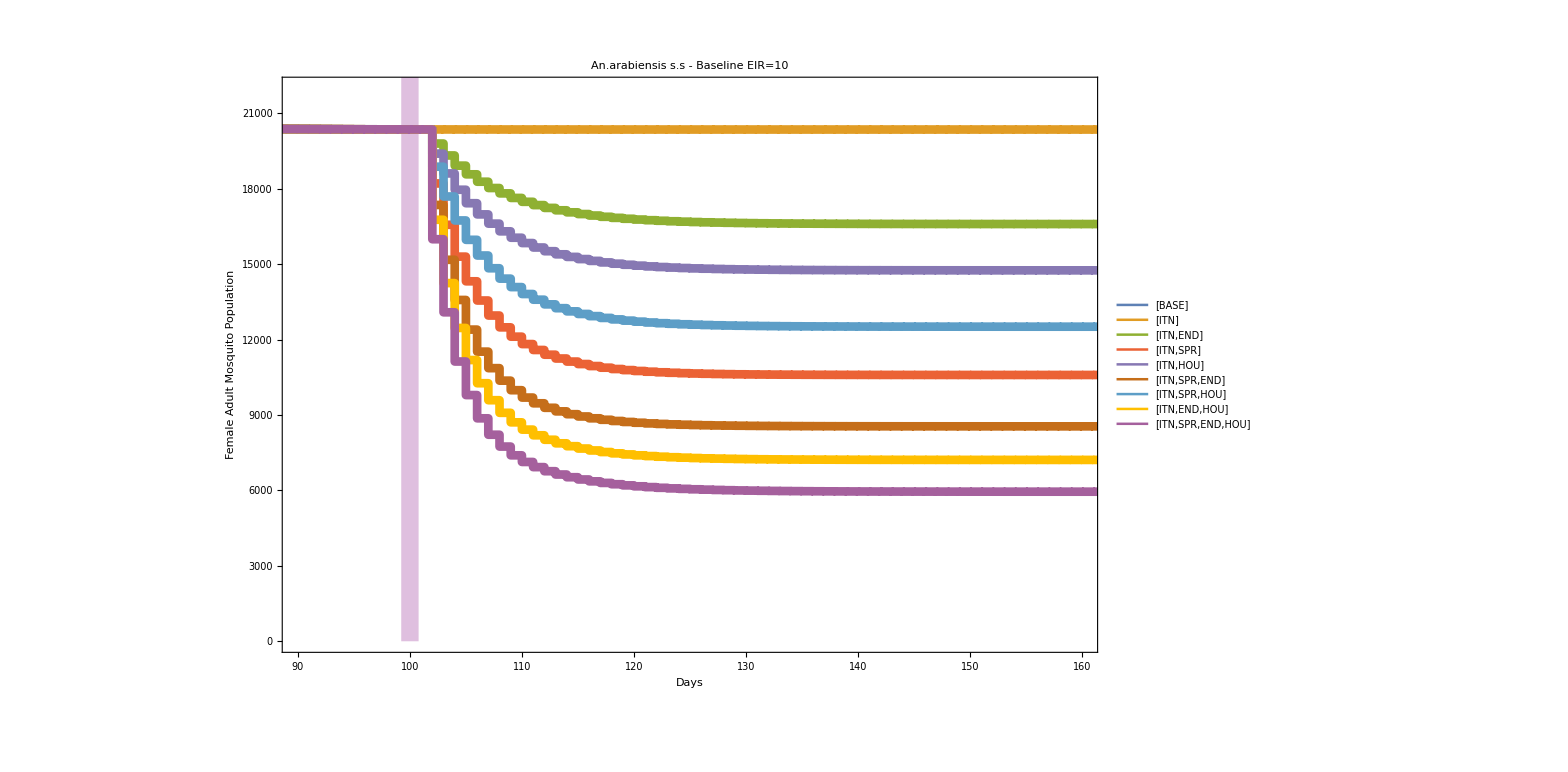

```mathematica
(**)
eirData=#[[All,4]]&/@dataList;
mosyData=(Total/@#[[All,1;;3]])&/@dataList;
(**)
ListLinePlot[mosyData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{0,150},{0,25000}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","Female Adult Mosquito Population"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,100000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,100000}}]}
]
Export["AATimeSeries_FullM.png",%,ImageResolution->300];
(**)
ListLinePlot[mosyData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{90,160},{0,22000}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","Female Adult Mosquito Population"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,100000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,100000}}]}
]
Export["AATimeSeries_ZoomM.png",%,ImageResolution->300];
```

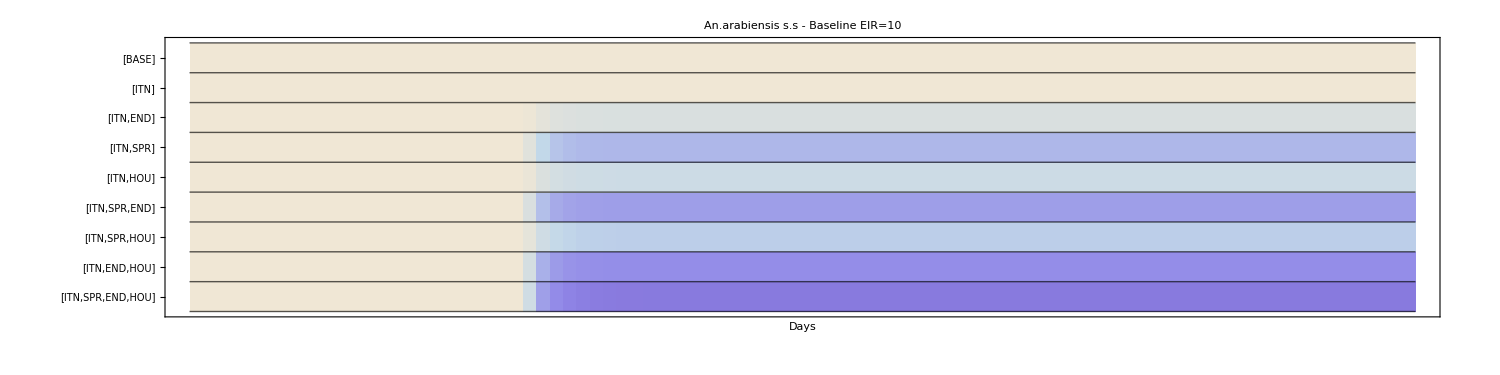

```mathematica
MatrixPlot[mosyData,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,20000}]]&),
ColorFunctionScaling->False,
ImageSize->1500,
BaseStyle->Directive[20],
PlotLegends->Placed[Automatic,Below],
FrameTicks->{{Transpose[{Range[Length[orderedLabels]],orderedLabels}],None},{None,Automatic}},
AspectRatio->.25,
LabelStyle->20,
Mesh->{Table[{i,Directive[Thick,Black,Opacity[.65]]},{i,0,10}],None},
FrameLabel->{None,"Days"},
FrameStyle->Directive[Gray,Thickness[.005]](*,
Epilog->{Red,Opacity[.25],Thickness[.0075],Line[{{25,0},{25,100}}],Purple,Opacity[.25],Thickness[.0075],Line[{{100,0},{100,10000}}]}*)
]
Export["AATimeSeries_MatrixM.png",%,ImageResolution->300];
```

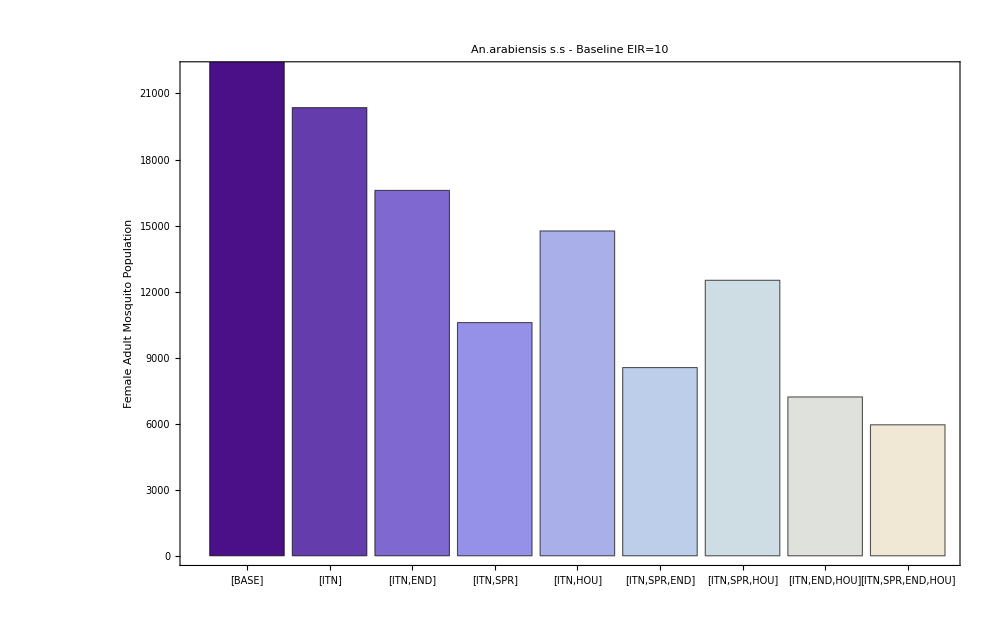

```mathematica
BarChart[Last/@mosyData,
ChartStyle->{EdgeForm[Directive[Thick,Black,Opacity[.65]]],"LakeColors"},
ChartLabels->(Rotate[#,90Degree]&/@orderedLabels),
FrameStyle->Thickness[.0075],
BaseStyle->20,
PlotLabel->"An.arabiensis s.s - Baseline EIR=10",
Frame->True,
FrameTicksStyle->20,
FrameLabel->{"","Female Adult Mosquito Population"},
ImageSize->1000,
PlotRange->{0,22000}
]
Export["AAHistogramM.png",%,ImageResolution->300];
```

## Load 100

Load Data

```mathematica
(**)
levels0000=Import["./EIR_100/0_0_0_0_100.csv"][[2;;All,requiredIndices]];
levels7000=Import["./EIR_100/7_0_0_0_100.csv"][[2;;All,requiredIndices]];
levels7008=Import["./EIR_100/7_0_0_8_100.csv"][[2;;All,requiredIndices]];
levels7080=Import["./EIR_100/7_0_8_0_100.csv"][[2;;All,requiredIndices]];
levels7800=Import["./EIR_100/7_8_0_0_100.csv"][[2;;All,requiredIndices]];
levels7880=Import["./EIR_100/7_8_8_0_100.csv"][[2;;All,requiredIndices]];
levels7808=Import["./EIR_100/7_8_0_8_100.csv"][[2;;All,requiredIndices]];
levels7088=Import["./EIR_100/7_0_8_8_100.csv"][[2;;All,requiredIndices]];
levels7888=Import["./EIR_100/7_8_8_8_100.csv"][[2;;All,requiredIndices]];
dataList={levels0000,levels7000,levels7008,levels7080,levels7800,levels7880,levels7808,levels7088,levels7888};
orderedLabels={"[BASE]","[ITN]","[ITN,END]","[ITN,SPR]","[ITN,HOU]","[ITN,SPR,END]","[ITN,SPR,HOU]","[ITN,END,HOU]","[ITN,SPR,END,HOU]"};
```

EIR

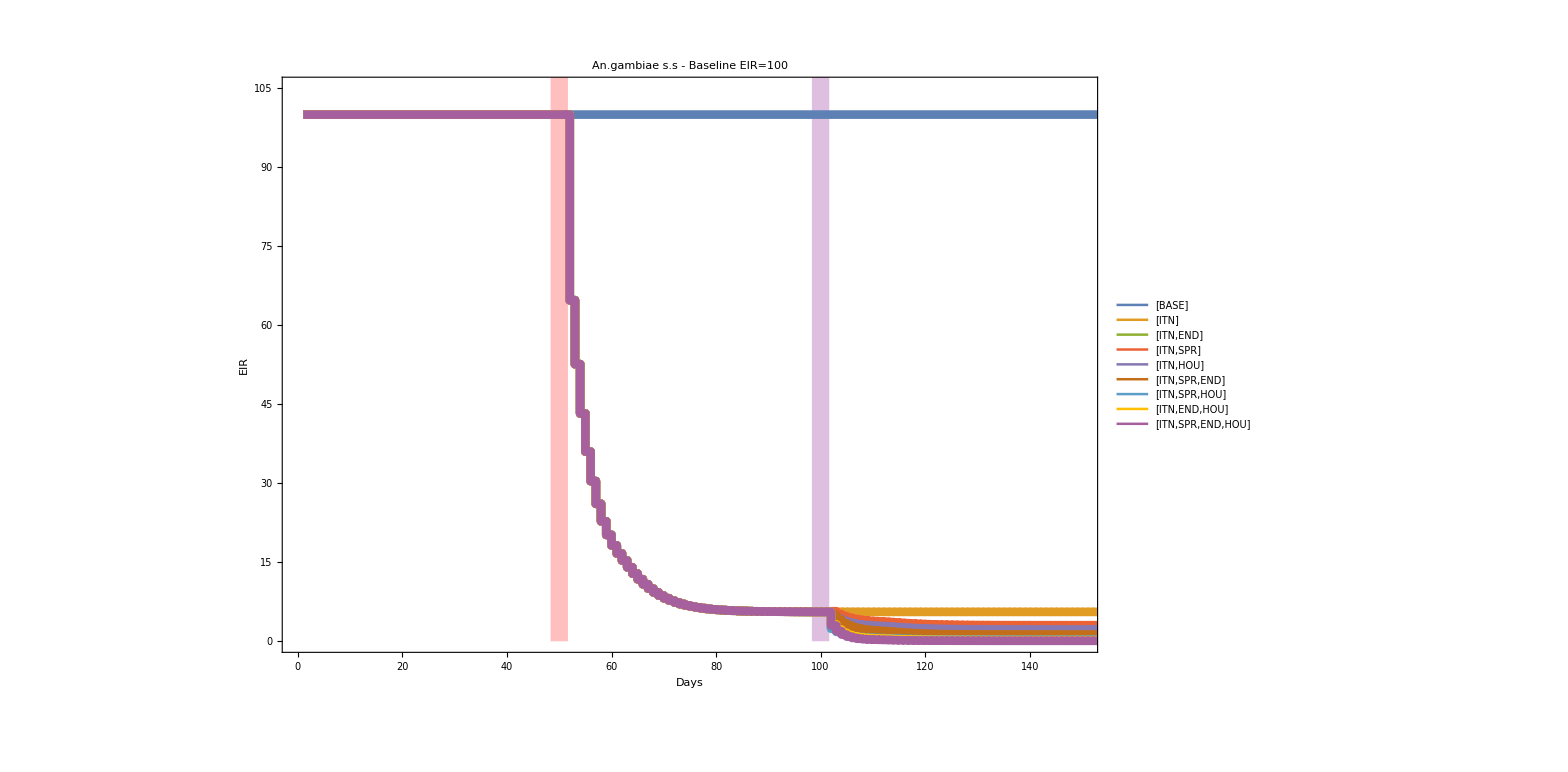

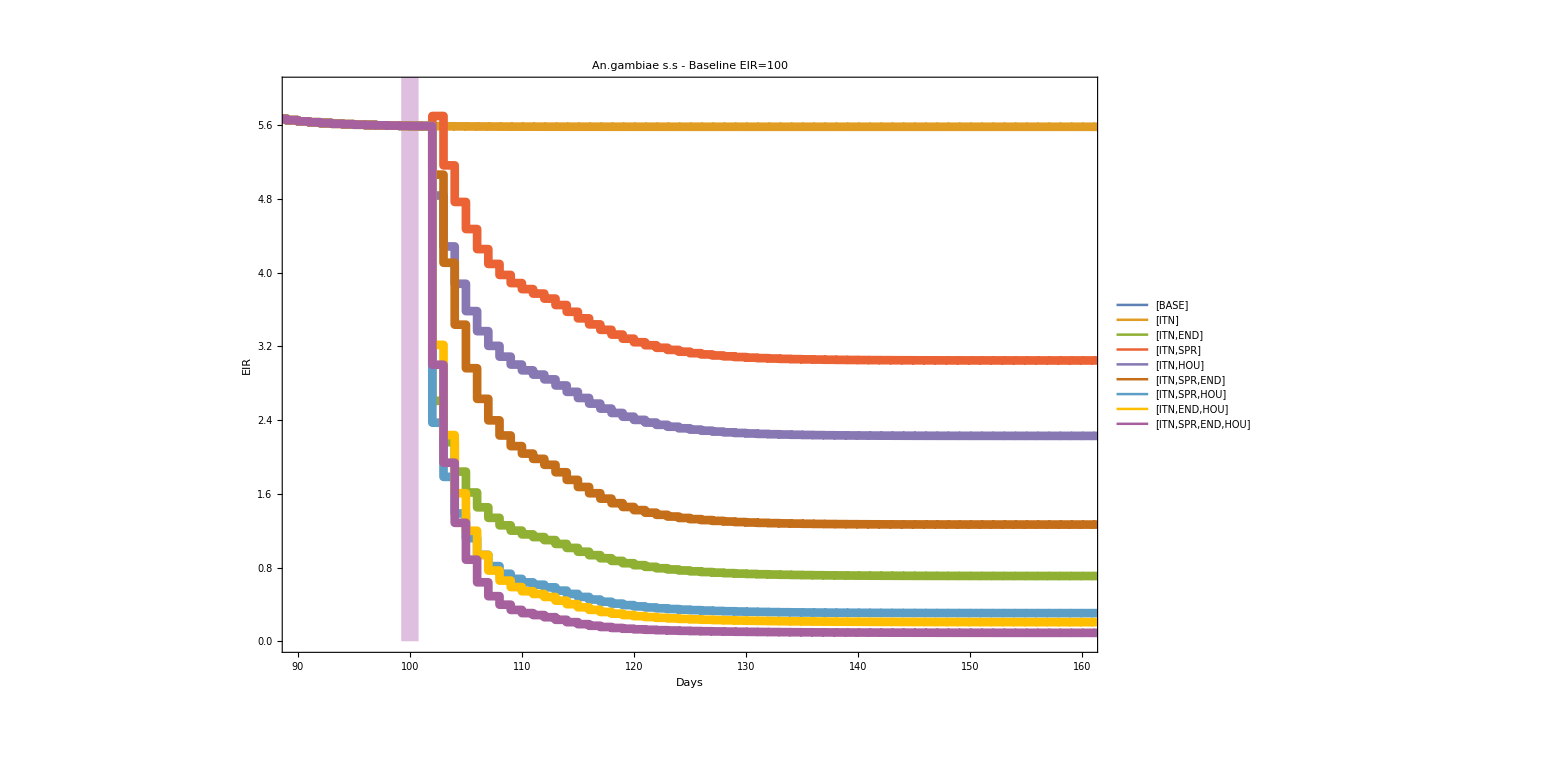

```mathematica
(**)
eirData=#[[All,4]]&/@dataList;
mosyData=(Total/@#[[All,1;;3]])&/@dataList;
(**)
ListLinePlot[eirData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{0,150},{0,105}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","EIR"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,10000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,10000}}]}
]
Export["AGTimeSeries_Full.png",%,ImageResolution->300];
(**)
ListLinePlot[eirData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{90,160},{0,6}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","EIR"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,10000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,10000}}]}
]
Export["AGTimeSeries_Zoom.png",%,ImageResolution->300];
```

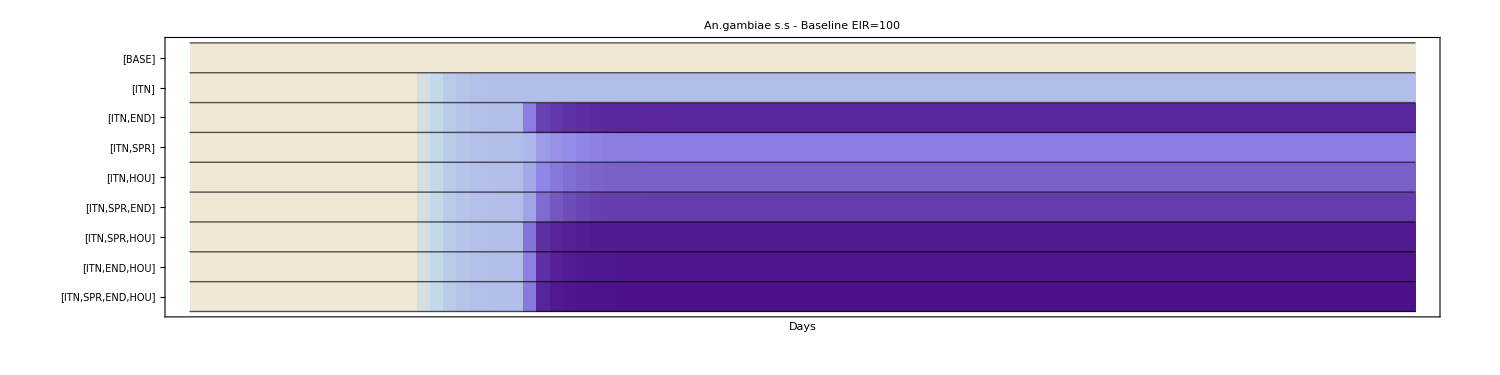

```mathematica
MatrixPlot[eirData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,10}]]&),
ColorFunctionScaling->False,
ImageSize->1500,
BaseStyle->Directive[20],
PlotLegends->Placed[Automatic,Below],
FrameTicks->{{Transpose[{Range[Length[orderedLabels]],orderedLabels}],None},{None,Automatic}},
AspectRatio->.25,
LabelStyle->20,
Mesh->{Table[{i,Directive[Thick,Black,Opacity[.65]]},{i,0,10}],None},
FrameLabel->{None,"Days"},
FrameStyle->Directive[Gray,Thickness[.005]](*,
Epilog->{Red,Opacity[.25],Thickness[.0075],Line[{{25,0},{25,100}}],Purple,Opacity[.25],Thickness[.0075],Line[{{100,0},{100,10000}}]}*)
]
Export["AGTimeSeries_Matrix.png",%,ImageResolution->300];
```

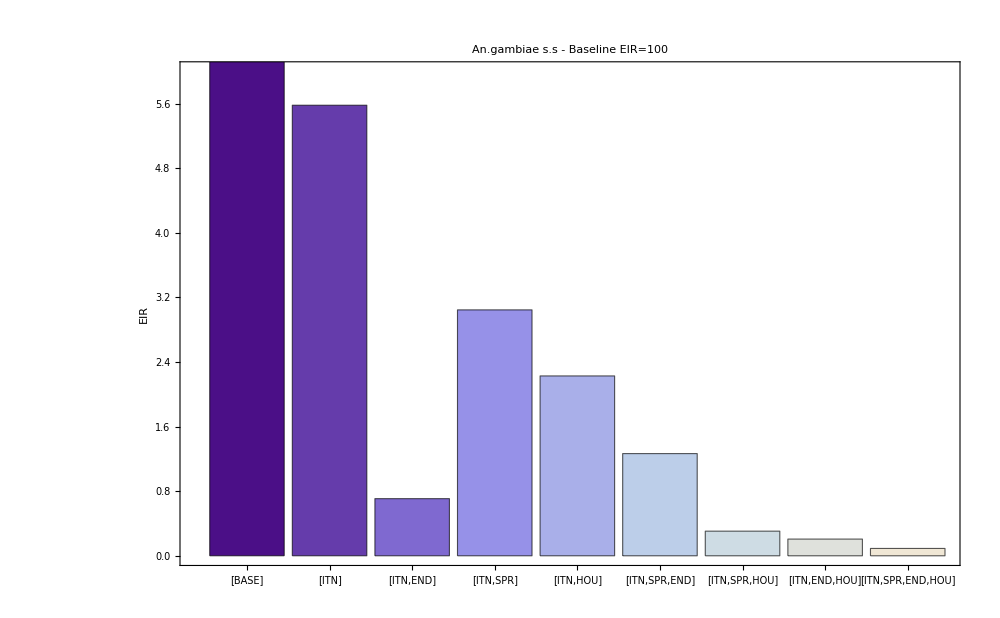

```mathematica
BarChart[Last/@eirData,
ChartStyle->{EdgeForm[Directive[Thick,Black,Opacity[.65]]],"LakeColors"},
ChartLabels->(Rotate[#,90Degree]&/@orderedLabels),
FrameStyle->Thickness[.0075],
BaseStyle->20,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameTicksStyle->20,
FrameLabel->{"","EIR"},
ImageSize->1000,
PlotRange->{0,6}
]
Export["AGHistogram.png",%,ImageResolution->300];
```

MOSSY

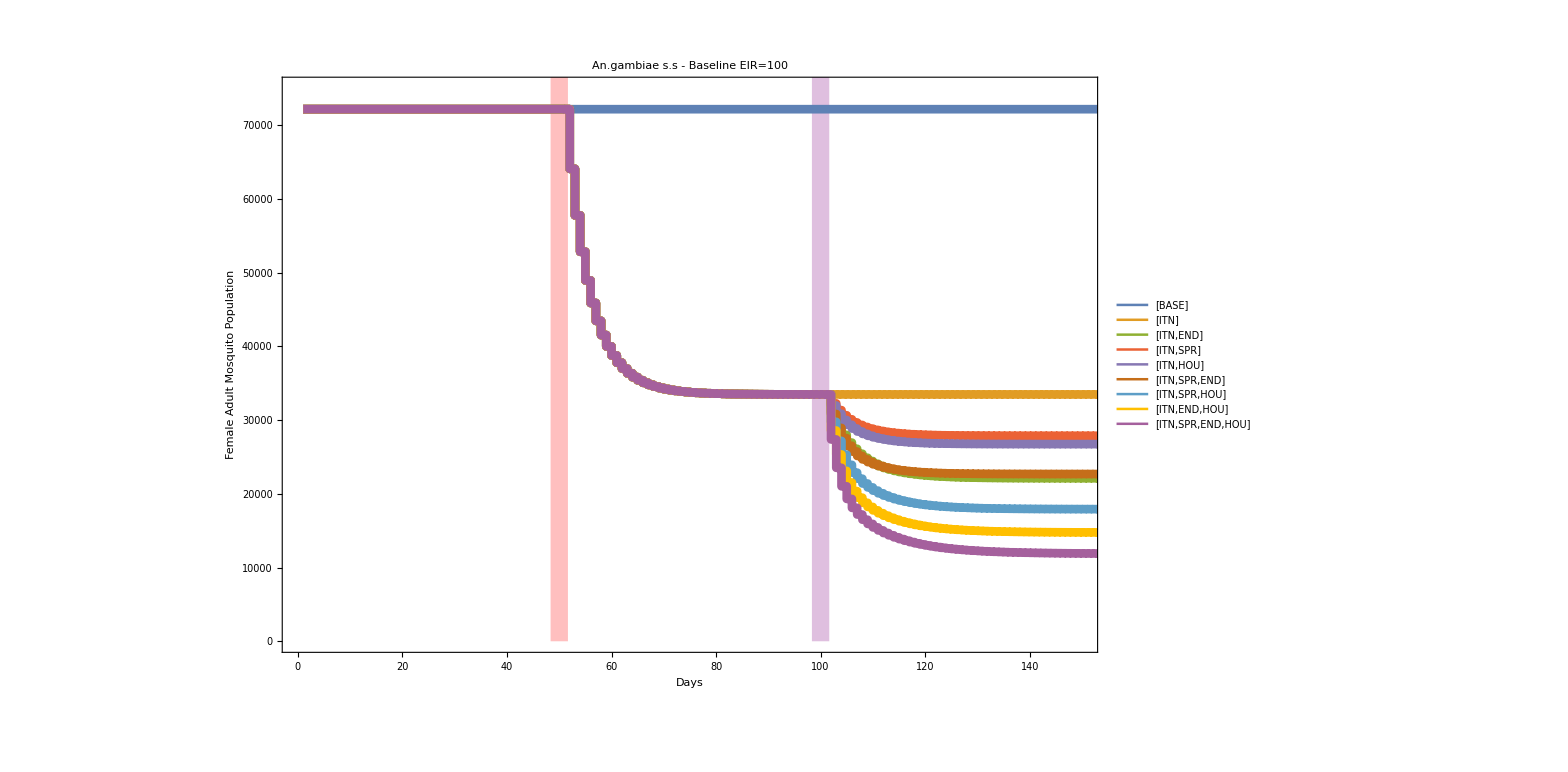

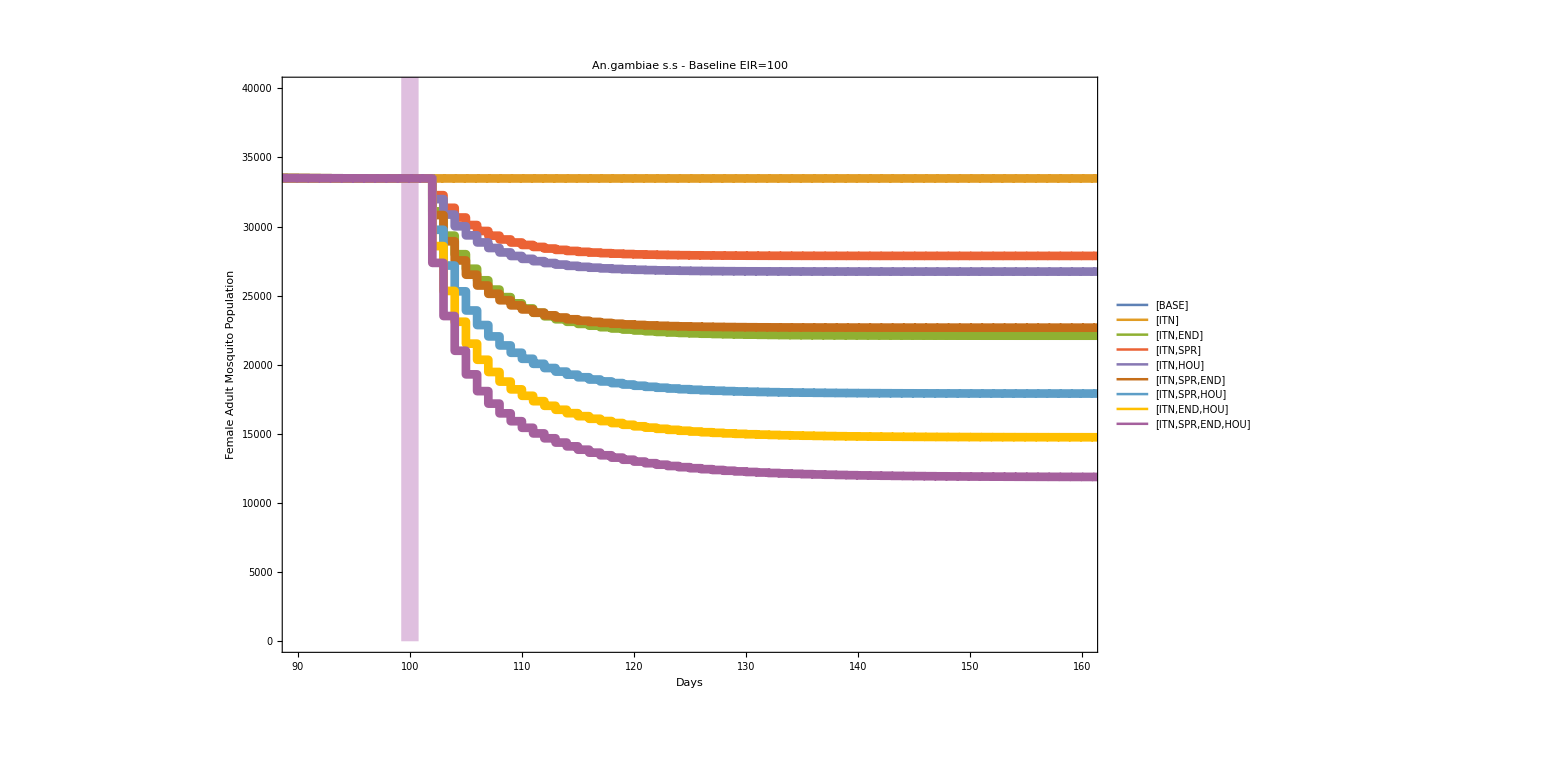

```mathematica
(**)
eirData=#[[All,4]]&/@dataList;
mosyData=(Total/@#[[All,1;;3]])&/@dataList;
(**)
ListLinePlot[mosyData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{0,150},{0,75000}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","Female Adult Mosquito Population"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,100000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,100000}}]}
]
Export["AGTimeSeries_FullM.png",%,ImageResolution->300];
(**)
ListLinePlot[mosyData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameStyle->Directive[Thickness[.0075],Gray],
LabelStyle->30,
PlotLegends->orderedLabels,
PlotRange->{{90,160},{0,40000}},
InterpolationOrder->0,
PlotStyle->Thickness[.005],
ImageSize->1250,
FrameLabel->{"Days","Female Adult Mosquito Population"},
Prolog->{Red,Opacity[.25],Thickness[.01],Line[{{50,0},{50,100000}}],Purple,Opacity[.25],Thickness[.01],Line[{{100,0},{100,100000}}]}
]
Export["AGTimeSeries_ZoomM.png",%,ImageResolution->300];
```

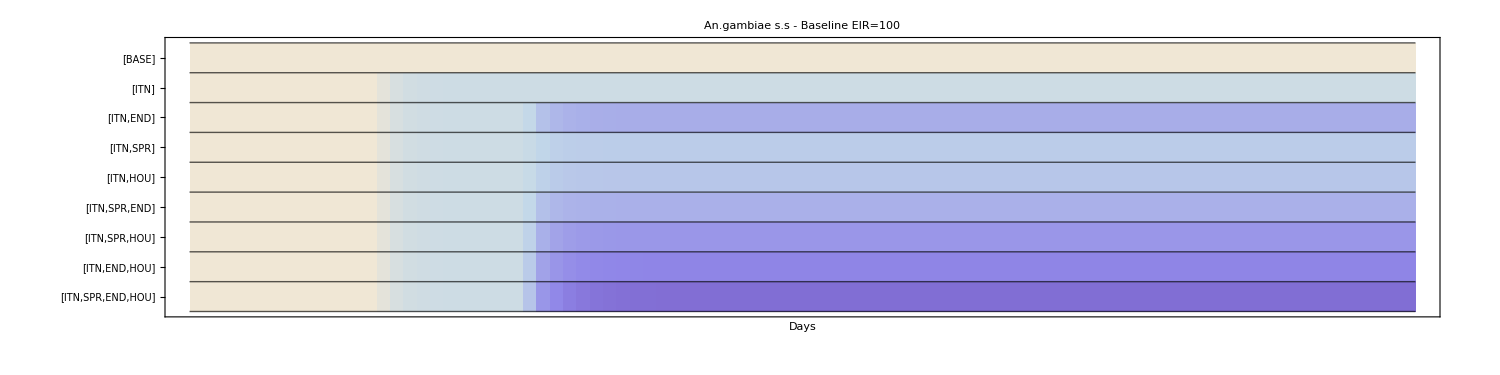

```mathematica
MatrixPlot[mosyData,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
ColorFunction->(ColorData["LakeColors"][Rescale[#,{0,45000}]]&),
ColorFunctionScaling->False,
ImageSize->1500,
BaseStyle->Directive[20],
PlotLegends->Placed[Automatic,Below],
FrameTicks->{{Transpose[{Range[Length[orderedLabels]],orderedLabels}],None},{None,Automatic}},
AspectRatio->.25,
LabelStyle->20,
Mesh->{Table[{i,Directive[Thick,Black,Opacity[.65]]},{i,0,10}],None},
FrameLabel->{None,"Days"},
FrameStyle->Directive[Gray,Thickness[.005]](*,
Epilog->{Red,Opacity[.25],Thickness[.0075],Line[{{25,0},{25,100}}],Purple,Opacity[.25],Thickness[.0075],Line[{{100,0},{100,10000}}]}*)
]
Export["AGTimeSeries_MatrixM.png",%,ImageResolution->300];
```

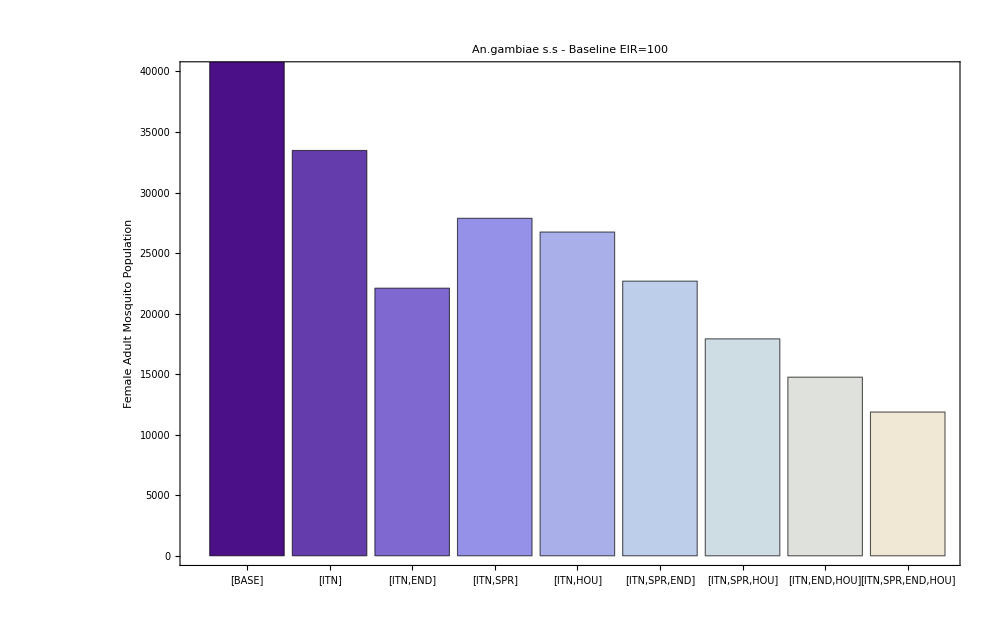

```mathematica
BarChart[Last/@mosyData,
ChartStyle->{EdgeForm[Directive[Thick,Black,Opacity[.65]]],"LakeColors"},
ChartLabels->(Rotate[#,90Degree]&/@orderedLabels),
FrameStyle->Thickness[.0075],
BaseStyle->20,
PlotLabel->"An.gambiae s.s - Baseline EIR=100",
Frame->True,
FrameTicksStyle->20,
FrameLabel->{"","Female Adult Mosquito Population"},
ImageSize->1000,
PlotRange->{0,40000}
]
Export["AGHistogramM.png",%,ImageResolution->300];
```